```mathematica
f[Ω_, z_]:= 1/((Ω (1+z)^3+(1-Ω)(1+z)^(3/2))^(1/2));
```

```mathematica
integrateFunction[Ω_?NumericQ,z0_?NumericQ]:=NIntegrate[f[Ω,z],{z,0,z0}];
```

```mathematica
ΩValues={0,0.3,0.7,1};
```

```mathematica
(*Generate a plot for each Ω*)
plots=Table[
Plot[
integrateFunction[i,z0],{z0,0,1},
PlotStyle->ColorData[97,"ColorList"][[i]],
AxesLabel->{"z","Integration Result"},
Frame->True,
FrameLabel->{{"Integration Result",None},{"z",None}},
LabelStyle->{FontSize->14},
PlotRange->All,
PlotLegends->Placed[
{"Ω = "<>ToString[ΩValues[[i]]]},{0.7,0.1}
]
],
{i,Length[ΩValues]}
];
```

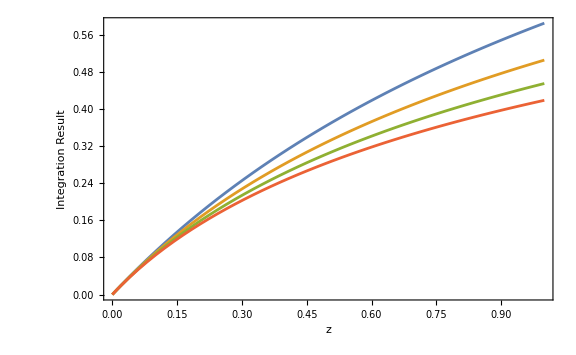

```mathematica
combinedPlot=Show[plots,PlotRange->All,ImageSize->Large]
```

```mathematica
Export["/Users/yaronetokayer/Yale Drive/Classes/PHYS 600/phys600 hw/phys600 hw 1/combined_plot.png",combinedPlot];
```